```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\tonnam_backup\Research_scratch\PVP5_EG_Ag\100Ag\10_pmf_curve\equilibrate\2_NPT_genIC

```mathematica
log=OpenRead["thermo.lammps"]
```

InputStream[thermo.lammps,66]

```mathematica
Find[log,"Step PotEng"]
```

# Step PotEng KinEng TotEng Temp Volume Press Lx Lz Pxx Pyy Pzz

```mathematica
thermo=ReadList[log,{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}]
```

{{6672001,-2631.89,250.342,-2381.55,296.999,65341.5,-808.914,24.3204,110.471,-1231.3,-10.8443,-1184.6},«998»,{6673000,-2637.72,247.364,-2390.35,293.466,64887.9,683.884,24.2644,110.211,72.212,1542.54,436.903}}

```mathematica
Close[log];
```

```mathematica
CreateDirectory["graph"];
```

```mathematica
Nearest[thermo[[All,7]],1]
```

{1.02963}

```mathematica
Position[thermo[[All,7]],Nearest[thermo[[All,7]],1][[1]]]
```

{{922}}

```mathematica
chosentimestep=thermo[[Flatten[Position[thermo[[All,7]],Nearest[thermo[[All,7]],1][[1]]]]]]
```

{{6672922,-2643.28,251.38,-2391.9,298.23,64967.1,1.02963,24.2784,110.218,483.474,-375.588,-104.796}}

```mathematica
Export["report.txt",{"Chosen timestep:",chosentimestep[[1,1]]," ","Pressure:",chosentimestep[[1,7]]}]
```

report.txt

```mathematica
timeprod=1;
thermotimestep=1;
timestepps=0.001;
```

```mathematica
Tavg=Mean[thermo[[All,5]]]
```

299.591

```mathematica
Tstd=StandardDeviation[thermo[[All,5]]]
```

3.41107

```mathematica
TStdErr=Tstd/(Length[thermo])^0.5
```

0.107868

```mathematica
Tavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],5]]]
```

299.591

```mathematica
Tstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],5]]]
```

3.41107

```mathematica
TStdErr2=Tstd2/(Length[thermo[[timeprod/thermotimestep;;Length[thermo],5]]])^0.5
```

0.107868

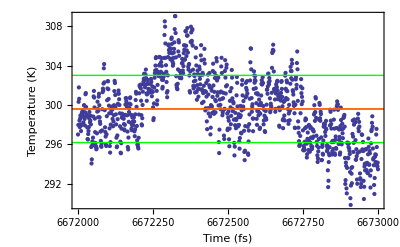

```mathematica
Tprofile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,5]]],2],1;;-1]],Plot[{Tavg,Tavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Tavg2+Tstd2,Tavg2-Tstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Temperature (K)"}]
```

```mathematica
Export["graph/Temp_profile.png",Tprofile,ImageResolution->100]
```

graph/Temp_profile.png

```mathematica
Pavg=Mean[thermo[[All,7]]]
```

-18.0801

```mathematica
Pstd=StandardDeviation[thermo[[All,7]]]
```

546.911

```mathematica
PStdErr=Pstd/(Length[thermo])^0.5
```

17.2948

```mathematica
Pavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],7]]]
```

-18.0801

```mathematica
Pstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],7]]]
```

546.911

```mathematica
PStdErr2=Pstd2/(Length[thermo[[timeprod/thermotimestep;;Length[thermo],5]]])^0.5
```

17.2948

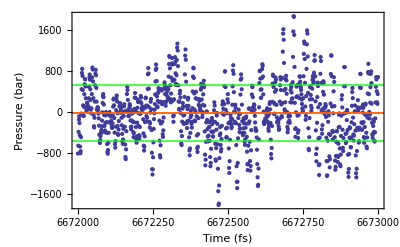

```mathematica
PProfile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,7]]],2],1;;-1]],Plot[{Pavg,Pavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Pavg2+Pstd2,Pavg2-Pstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Pressure (bar)"}]
```

```mathematica
Export["graph/Pressure_profile.png",PProfile,ImageResolution->100]
```

graph/Pressure_profile.png

```mathematica
Volavg=Mean[thermo[[All,6]]]
```

65147.7

```mathematica
Volstd=StandardDeviation[thermo[[All,6]]]
```

146.349

```mathematica
VolStdErr=Volstd/(Length[thermo])^0.5
```

4.62796

```mathematica
Volavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],6]]]
```

65147.7

```mathematica
Volstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],6]]]
```

146.349

```mathematica
VolStdErr2=Volstd2/(Length[thermo[[timeprod/thermotimestep;;Length[thermo],5]]])^0.5
```

4.62796

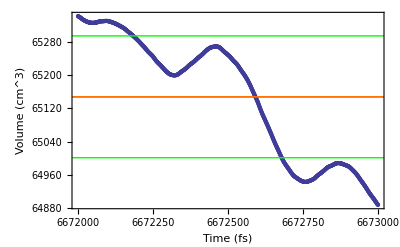

```mathematica
VProfile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,6]]],2],1;;-1]],Plot[{Volavg,Volavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Volavg2+Volstd2,Volavg2-Volstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Volume (cm^3)"}]
```

```mathematica
Export["graph/Volume_profile.png",VProfile,ImageResolution->100]
```

graph/Volume_profile.png

```mathematica
Engavg=Mean[thermo[[All,2]]]
```

-2633.46

```mathematica
Engstd=StandardDeviation[thermo[[All,2]]]
```

3.88345

```mathematica
EngStdErr=Engstd/(Length[thermo])^0.5
```

0.122805

```mathematica
Engavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],2]]]
```

-2633.46

```mathematica
Engstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],2]]]
```

3.88345

```mathematica
EngStdErr2=Engstd2/(Length[thermo[[timeprod/thermotimestep;;Length[thermo],5]]])^0.5
```

0.122805

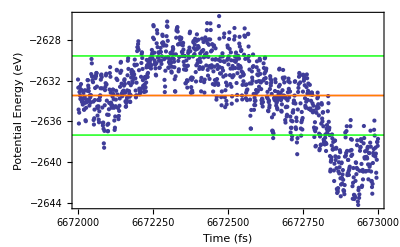

```mathematica
EProfile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,2]]],2],1;;-1]],Plot[{Engavg,Engavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Engavg2+Engstd2,Engavg2-Engstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Potential Energy (eV)"}]
```

```mathematica
Export["graph/Energy_profile.png",EProfile,ImageResolution->100]
```

graph/Energy_profile.png

```mathematica
Lzavg=Mean[thermo[[All,9]]]
```

110.043

```mathematica
Lzstd=StandardDeviation[thermo[[All,9]]]
```

0.133133

```mathematica
Lzavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],9]]]
```

110.043

```mathematica
Lzstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],9]]]
```

0.133133

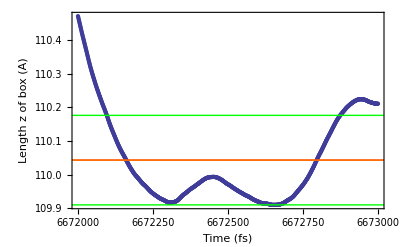

```mathematica
LzProfile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,9]]],2],1;;-1]],Plot[{Lzavg,Lzavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Lzavg2+Lzstd2,Lzavg2-Lzstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Length z of box (A)"}]
```

```mathematica
Export["graph/Lz_profile.png",LzProfile,ImageResolution->100]
```

graph/Lz_profile.png

```mathematica
Lxavg=Mean[thermo[[All,8]]]
```

24.3315

```mathematica
Lxstd=StandardDeviation[thermo[[All,8]]]
```

0.0310464

```mathematica
Lxavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],8]]]
```

24.3315

```mathematica
Lxstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],8]]]
```

0.0310464

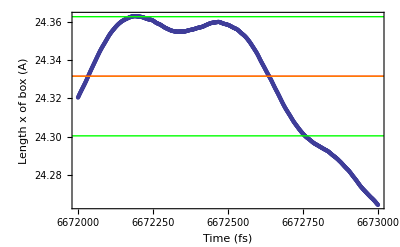

```mathematica
LxProfile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,8]]],2],1;;-1]],Plot[{Lxavg,Lxavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Lxavg2+Lxstd2,Lxavg2-Lxstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Length x of box (A)"}]
```

```mathematica
Export["graph/Lx_profile.png",LxProfile,ImageResolution->100]
```

graph/Lx_profile.png